```mathematica
GenerateAllGraphsOfSize2[k_]:=Block[{edges=Subsets[Range[k],{2}],combinations, total, current,result},

combinations=Subsets[edges];
total=Length[combinations];
current=0;
Monitor[
result=Select[
Table[
current++;
Graph[Range[k],e, VertexLabels->"Name"],
{e,combinations}
],
ConnectedGraphQ[#]&
],
{current,total}
];
PrintTemporary["Graphs found ", k, " --", Length[result]];
result
]
```

```mathematica
gr=ReadList["D:\\Users\\alfredo\\Google\\Math\\ConvertGraphs\\ConvertGraphs\\graphs8.txt"];
```

```mathematica
Length[gr]
```

11116

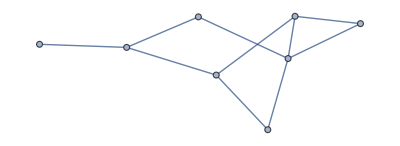
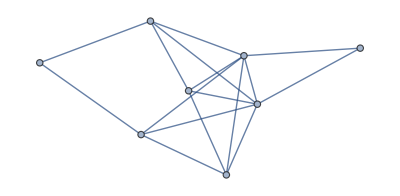
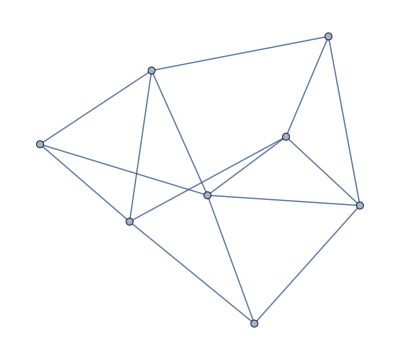
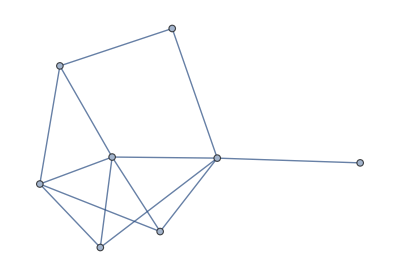
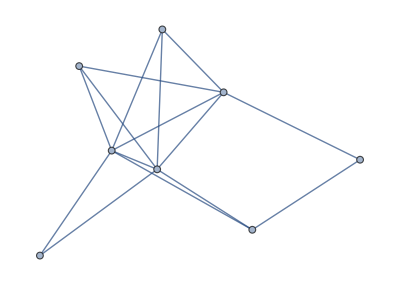
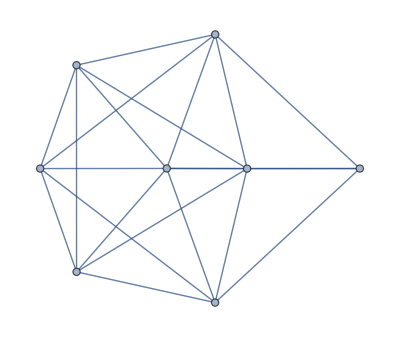
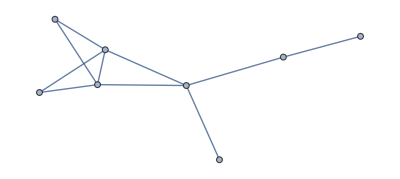
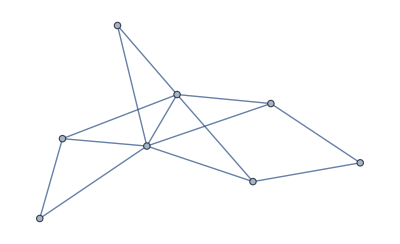

```mathematica
Map[Graph[DeleteDuplicates[Sort/@#]]&,RandomSample[gr,20]]
```

```mathematica
ChromaticPolynomial[-Graphics-,x]
```

-20 x+88 x^2-165 x^3+173 x^4-111 x^5+44 x^6-10 x^7+x^8

```mathematica
Expand[x(x-1)(x-2)(x-3)(x-4)^4]
```

-1536 x+4352 x^2-4928 x^3+2944 x^4-1014 x^5+203 x^6-22 x^7+x^8

```mathematica
found=Select[Map[Graph[DeleteDuplicates[Sort/@#]]&,gr],ChromaticPolynomial[#,x]==-1536 x+4352 x^2-4928 x^3+2944 x^4-1014 x^5+203 x^6-22 x^7+x^8&];
```

```mathematica
Length[found]
```

5

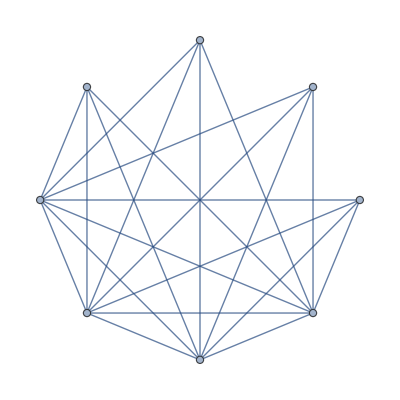
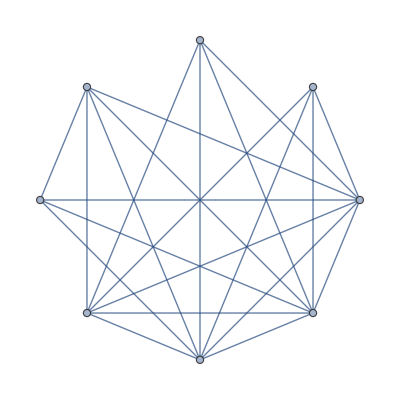
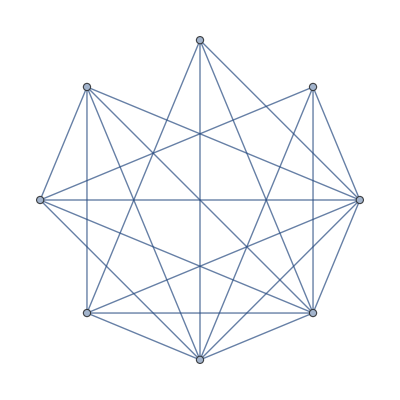
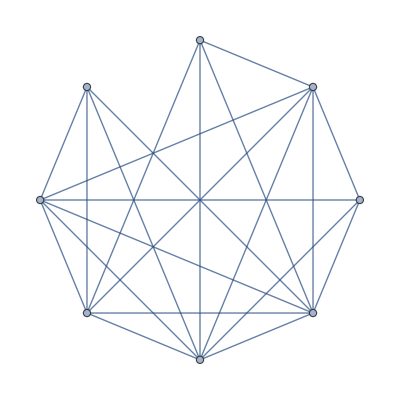
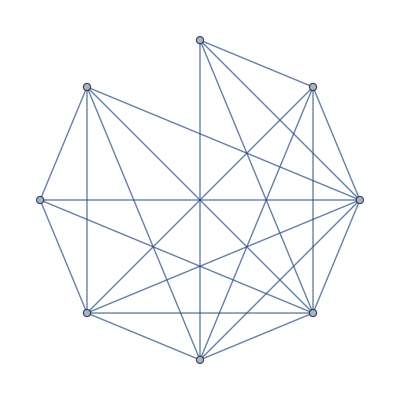
{-Graphics-22,-Graphics-22,-Graphics-22,-Graphics-22,-Graphics-22}

```mathematica
Map[With[{g=Graph[#,GraphLayout->"CircularEmbedding"]},Labeled[g,EdgeCount[g]]]&,found]
```

```mathematica
DeleteDuplicates[Sort/@gr[[1]]]
```

{0<->7,1<->7,2<->7,3<->7,4<->7,5<->7,6<->7}

```mathematica
AdjacencyMatrix[Graph[gr[[1]]]]/2//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
D:\Users\alfredo\Google\Math\ConvertGraphs\ConvertGraphs\graphs8.txt
```

## Now for seven

```mathematica
Expand[x(x-1)(x-2)(x-3)(x-4)^3]
```

384 x-992 x^2+984 x^3-490 x^4+131 x^5-18 x^6+x^7

```mathematica
found2=Select[Map[VertexDelete[Graph[DeleteDuplicates[Sort/@#]],7]&,gr],ChromaticPolynomial[#,x]==384 x-992 x^2+984 x^3-490 x^4+131 x^5-18 x^6+x^7&];
```

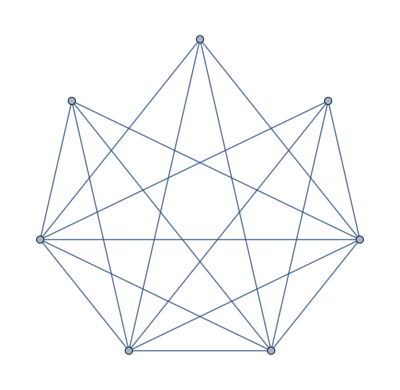
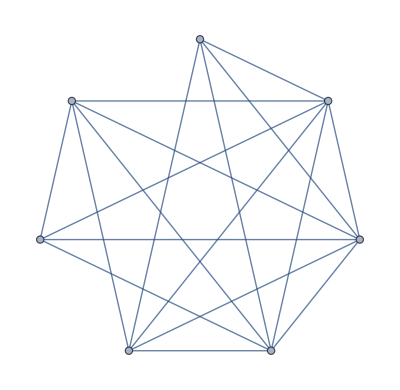
{-Graphics-18,-Graphics-18}

```mathematica
Map[With[{g=Graph[#,GraphLayout->"CircularEmbedding"]},Labeled[g,EdgeCount[g]]]&,found2]
```

## Now six

```mathematica
Expand[x(x-1)(x-2)(x-3)(x-4)^2]
```

-96 x+224 x^2-190 x^3+75 x^4-14 x^5+x^6

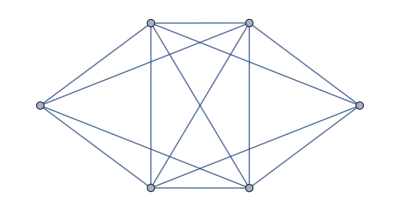

```mathematica
found3=Select[Map[VertexDelete[VertexDelete[Graph[DeleteDuplicates[Sort/@#]],7],6]&,gr],ChromaticPolynomial[#,x]==-96 x+224 x^2-190 x^3+75 x^4-14 x^5+x^6&]
```

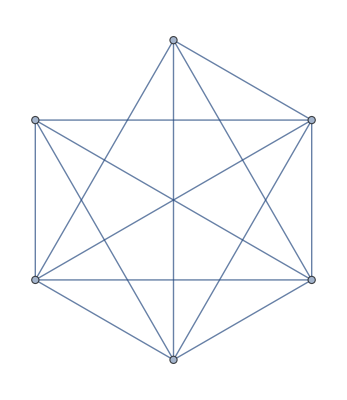
{-Graphics-14}

```mathematica
Map[With[{g=Graph[#,GraphLayout->"CircularEmbedding"]},Labeled[g,EdgeCount[g]]]&,found3]
```

```mathematica
Expand[x(x-1)(x-2)(x-3)^3]
```

-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6

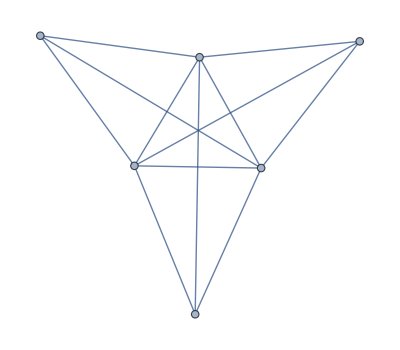
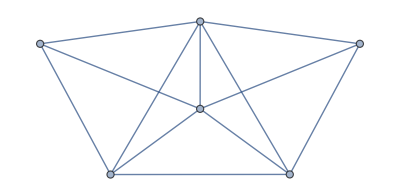

```mathematica
found4=Select[Map[VertexDelete[VertexDelete[Graph[DeleteDuplicates[Sort/@#]],7],6]&,gr],ChromaticPolynomial[#,x]==-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6&]
```

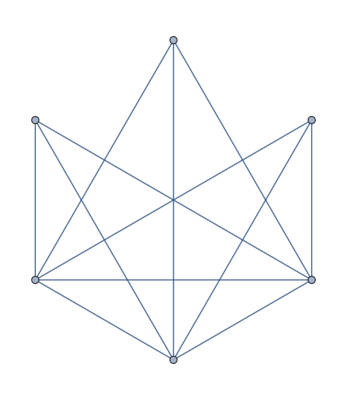
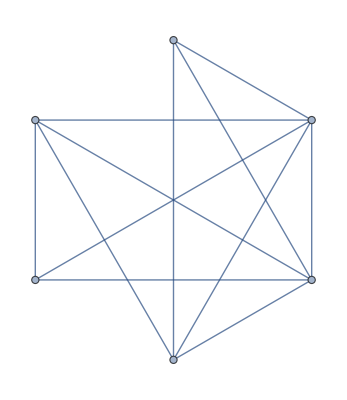
{-Graphics-12,-Graphics-12}

```mathematica
Map[With[{g=Graph[#,GraphLayout->"CircularEmbedding"]},Labeled[g,EdgeCount[g]]]&,found4]
```

```mathematica
EdgeCount[CompleteGraph[6]]
```

15

```mathematica
3*6-6
```

12

```mathematica
Map[MaximalPlanarQ,found4]
```

{False,True}

```mathematica
Tally[found4,IsomorphicGraphQ]
```

{{-Graphics-,1},{-Graphics-,1}}

```mathematica
Expand[x(x-1)(x-2)(x-3)^4]
```

162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7

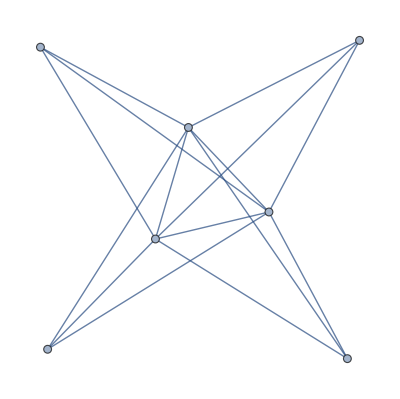
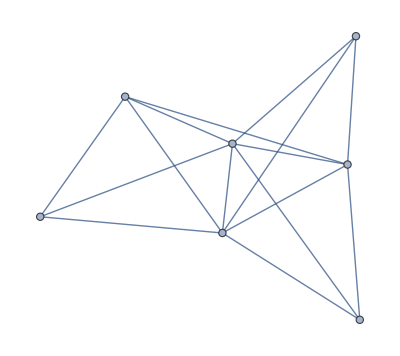
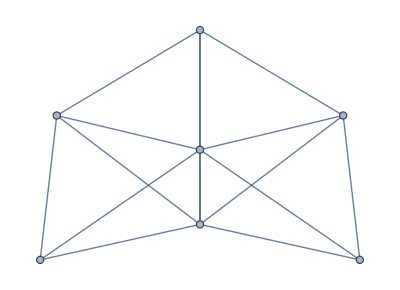
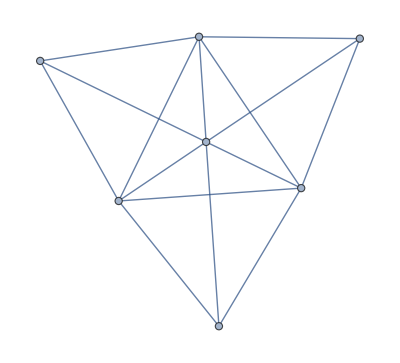
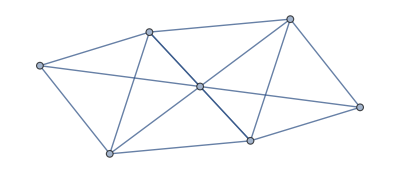

```mathematica
found5=Select[Map[VertexDelete[Graph[DeleteDuplicates[Sort/@#]],7]&,gr],ChromaticPolynomial[#,x]==162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7&]
```

```mathematica
Tally[found5,IsomorphicGraphQ]
```

{{-Graphics-,1},{-Graphics-,1},{-Graphics-,1},{-Graphics-,1},{-Graphics-,1}}

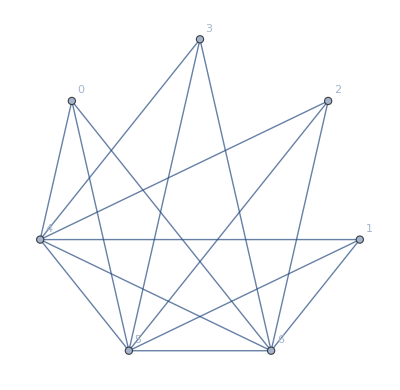
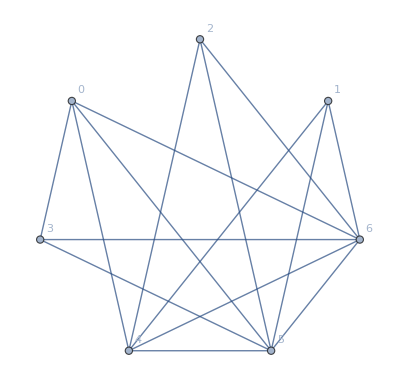
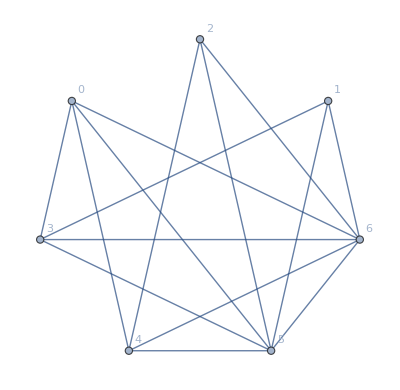
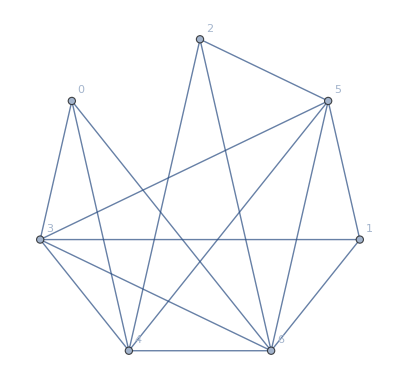
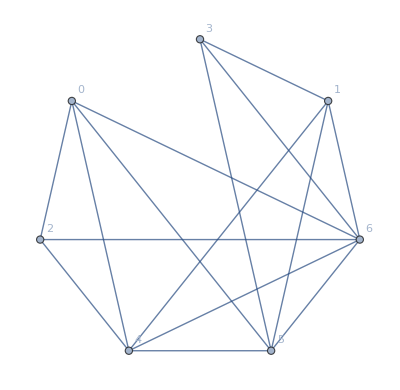
{-Graphics-15,-Graphics-15,-Graphics-15,-Graphics-15,-Graphics-15}

```mathematica
Map[With[{g=Graph[#,GraphLayout->"CircularEmbedding",VertexLabels->"Name"]},Labeled[g,EdgeCount[g]]]&,found5]
```

```mathematica
Map[MaximalPlanarQ,found5]
```

{False,False,True,True,True}

```mathematica
Map[FormulaLevels[FindFullFormula[#]]&,found5]
```

{{{4,1},{5,7},{6,6},{7,1}},{{4,1},{5,7},{6,6},{7,1}},{{4,1},{5,7},{6,6},{7,1}},{{4,1},{5,7},{6,6},{7,1}},{{4,1},{5,7},{6,6},{7,1}}}

```mathematica
FormulaGraphReverse[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s1]->SetsToSymbol[s2]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]->Rotate[ SymbolToLabel[ SetsToSymbol[s]],7Pi/6],{s,sets}];
Rotate[Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding",ImageSize->600],Pi]
]
```

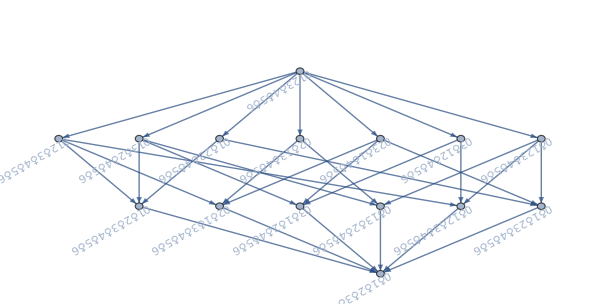
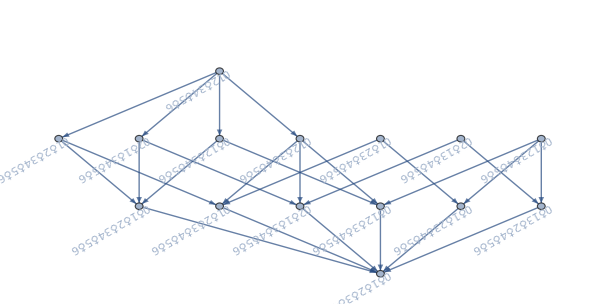
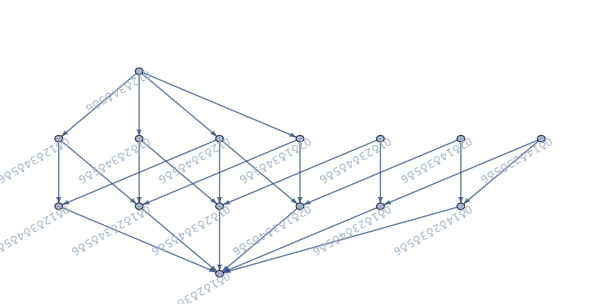
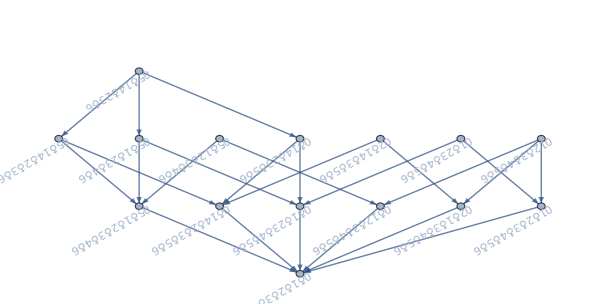
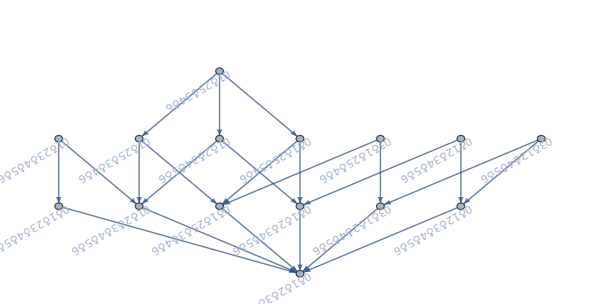
{-Graphics-False→7,-Graphics-False→7,-Graphics-True→7,-Graphics-True→7,-Graphics-True→7}

```mathematica
Map[Labeled[FormulaGraphReverse[Fold[Plus,FindFullFormula[#]]],MaximalPlanarQ[#]->VertexCount[#]]&,found5]
```

```mathematica
Expand[x(x-1)(x-2)(x-3)^5]
```

-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8

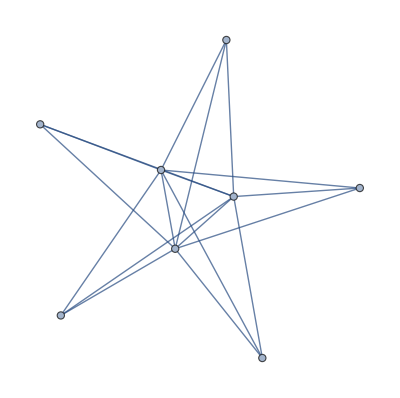
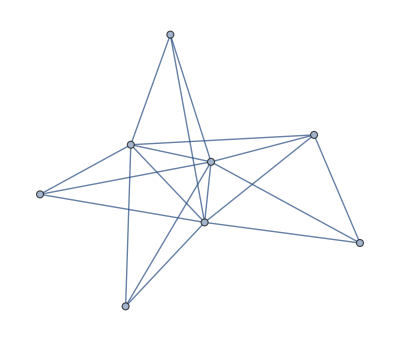
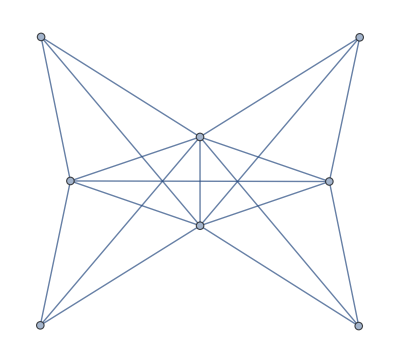
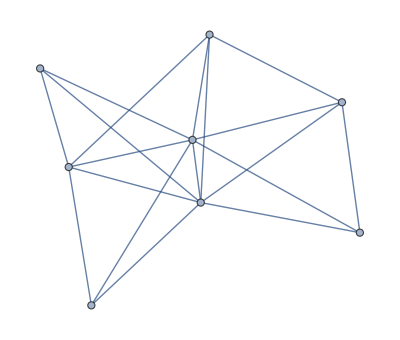
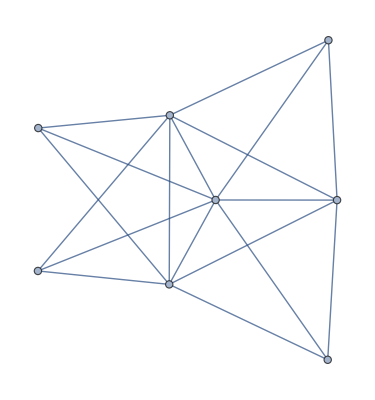
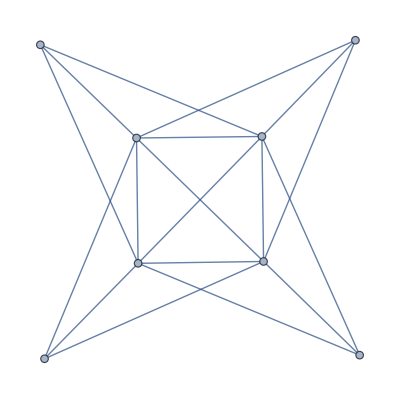
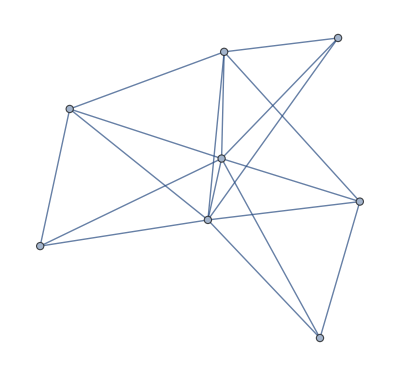
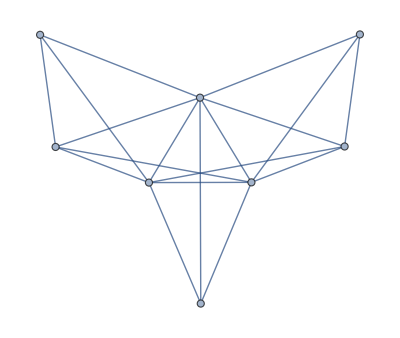

```mathematica
found6=Select[Map[Graph[DeleteDuplicates[Sort/@#]]&,gr],ChromaticPolynomial[#,x]==-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8&]
```

```mathematica
Map[FormulaLevels[FindFullFormula[#]]&,found6]//Tally
```

{{{{4,1},{5,15},{6,25},{7,10},{8,1}},15}}

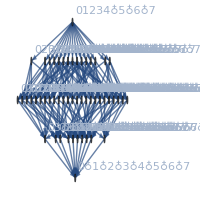
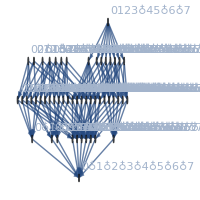
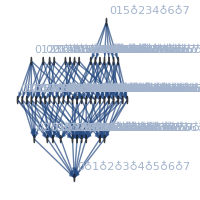
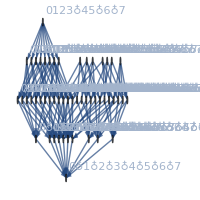
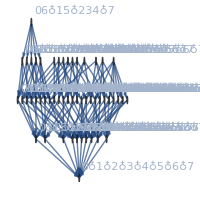
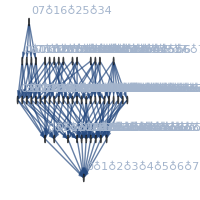
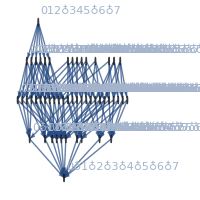
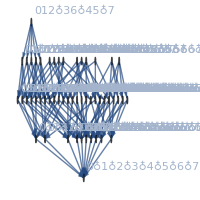
{-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-True,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-True,-Graphics-True,-Graphics-True,-Graphics-True,-Graphics-True,-Graphics-True}

```mathematica
Map[Labeled[FormulaGraphReverse[Fold[Plus,FindFullFormula[#]]],MaximalPlanarQ[#]]&,found6]
```

```mathematica
Table[PowerCoeff[ChromaticPolynomial[g,x],3],{g,found5}]
```

{{0,0,0,0,6,11,6,1},{0,0,0,0,6,11,6,1},{0,0,0,0,6,11,6,1},{0,0,0,0,6,11,6,1},{0,0,0,0,6,11,6,1}}

```mathematica
Table[
MatrixForm[Table[PowerCoeff[ChromaticPolynomial[g,x],3],{g,all}]]
,{all,{found,found2,found3,found4,found5,found6}}]
```

{(0 | 6 | -13 | -2 | 19 | -6 | -7 | 2 | 1
0 | 6 | -13 | -2 | 19 | -6 | -7 | 2 | 1
0 | 6 | -13 | -2 | 19 | -6 | -7 | 2 | 1
0 | 6 | -13 | -2 | 19 | -6 | -7 | 2 | 1
0 | 6 | -13 | -2 | 19 | -6 | -7 | 2 | 1),(0 | -6 | 7 | 9 | -10 | -4 | 3 | 1
0 | -6 | 7 | 9 | -10 | -4 | 3 | 1),(0 | 6 | -1 | -10 | 0 | 4 | 1),(0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 6 | 11 | 6 | 1),(0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 6 | 11 | 6 | 1),(0 | 0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 0 | 6 | 11 | 6 | 1)}

```mathematica
Expand[x(x-1)(x-2)(x-3)(x-4)^4]
```

-1536 x+4352 x^2-4928 x^3+2944 x^4-1014 x^5+203 x^6-22 x^7+x^8

```mathematica
found7=Select[Map[Graph[DeleteDuplicates[Sort/@#]]&,gr],ChromaticPolynomial[#,x]==-1536 x+4352 x^2-4928 x^3+2944 x^4-1014 x^5+203 x^6-22 x^7+x^8&];
```

```mathematica
Table[
MatrixForm[Table[PowerCoeff[ChromaticPolynomial[g,x],3],{g,all}]]
,{all,{found7}}]
```

{(0 | 6 | -13 | -2 | 19 | -6 | -7 | 2 | 1
0 | 6 | -13 | -2 | 19 | -6 | -7 | 2 | 1
0 | 6 | -13 | -2 | 19 | -6 | -7 | 2 | 1
0 | 6 | -13 | -2 | 19 | -6 | -7 | 2 | 1
0 | 6 | -13 | -2 | 19 | -6 | -7 | 2 | 1)}

```mathematica
Table[
MatrixForm[Table[PowerCoeff[ChromaticPolynomial[g,x],4],{g,all}]]
,{all,{found7}}]
```

{(0 | 0 | 0 | 0 | 24 | 50 | 35 | 10 | 1
0 | 0 | 0 | 0 | 24 | 50 | 35 | 10 | 1
0 | 0 | 0 | 0 | 24 | 50 | 35 | 10 | 1
0 | 0 | 0 | 0 | 24 | 50 | 35 | 10 | 1
0 | 0 | 0 | 0 | 24 | 50 | 35 | 10 | 1)}